# Numerical solution for the Hanle -system.

```mathematica
Clear["Global`*"]
```

### Constants and Parameters

```mathematica
kB=1.38 10^-23;(*Boltzmann-constant*)
T=273+21; (*temperature of the cell*)
c=3 10^8; (*Speed of light*)
d12=3.5 10^-29; (*dipole-moment for D2 line Rb*)
hbar= 1.054 10^-34; 
ep0=8.854 10^-12;
mass=1.443 10^-27;
muB=9.274*10^-28;(*J G^-1 Bohr's magneton*)
Γ= 2π  6 10^6;(*Spontaneous decay rate*)
gF=0.5;
g1= gF muB/hbar;
nmdens= 2 10^16;
c1= (2 nmdens d12^2)/(hbar ep0);
K = (2 π)/(780 10^-9);
lvc = 5 10^-3;
```

### Rabi frequency of the beam

```mathematica
rabif[power_]:= Module[{p=power},
dia =2 10^-3;
area = π dia^2/4;
intensity = 2 (p 10^-6)/area;
E0 = √((2 intensity)/(ep0 c));
(d12 E0)/hbar]
Ωc = rabif[0]
```

0.

### Time of flight decay rate

```mathematica
tof[dia_]:= Module[{d=dia},
vth = √((8 kB T)/(π mass));
10^3 vth/d
]
γ =tof[4]
```

668945.

### Hamiltonian, density matrix and decay matrix

```mathematica
rho = {{r11, r12, r13, r14},{r21, r22, r23,  r24}, {r31, r32, r33, r34}, {r41, r42, r43,r44}};
rho1 = Flatten[rho];
H={{  g1 (B+0.2) ,(g1 B1)/(√2)Exp[-I theta],0,- Ωc/(2 √6)},{(g1 B1)/(√2)Exp[I theta],0,(g1 B1)/(√2)Exp[-I theta],(- Ωp)/(2 √3)},{0,(g1 B1)/(√2)Exp[I theta],-g1 B(B+0.2) ,(- Ωc)/(2 √6)},{ (- Ωc)/(2 √6),(- Ωp)/(2 √3),(- Ωc)/(2 √6),0}};
Λ= {{γ,0,0,0},{0,γ,0,0},{0,0,γ,0},{0,0,0,Γ+γ}};
repop = {{γ/3 +Γ/4 r44 ,0,0,0},{
0,γ/3 +Γ/2 r44,0,0},{0,0,γ/3 +Γ/4 r44,0},{0,0,0,0}};
comm =(H.rho - rho.H);
anticomm = Λ.rho +rho.Λ;
deph={{0, - γ1 r12, -  γ1 r13, 0},{- γ1 r21, 0, - γ1 r23, 0},{- γ1 r31, - γ1 r32, 0, 0},{0,0, 0,0}};
```

### Equations and Solutions

```mathematica
f[x0_,y0_,z0_]:=Module[{x=x0,y=y0,z=z0},

Ωp = rabif[x];
B1 =y;
n=2;
theta=π/180 z;
eqTable = Table[0==-I (comm[[i,j]])-1/2 anticomm[[i,j]]+repop[[i,j]],{i,1,4},{j,1,4}];
eqs = Join[Flatten[eqTable],{r11+r22+r33+r44==1}];
rho11 =Table[Re@Solve[eqs,rho1][[1,1,2]],{B,-n,n,(2n+1)/200}];
rho22=Table[Re@Solve[eqs,rho1][[1,6,2]],{B,-n,n,(2n+1)/200}];
rho33=Table[Re@Solve[eqs,rho1][[1,11,2]],{B,-n,n,(2n+1)/200}];
rho44=Table[Re@Solve[eqs,rho1][[1,16,2]],{B,-n,n,(2n+1)/200}];
irho24=Table[1-Im[Solve[eqs,rho1][[1,14,2]]],{B,-n,n,(2n+1)/200}];
rrho24=Table[Re[Solve[eqs,rho1][[1,8,2]]],{B,-n,n,(2n+1)/200}];
table0=Table[j,{j,-n,n,(2n+1)/200}];
p11=ListLinePlot[Table[{table0[[i]],rho11[[i]]},{i,1, Length[table0]}], PlotRange->All,Frame->True,PlotStyle->Black,FrameLabel->{"B_s(G)", "ρ11"},LabelStyle->Directive[Bold, Medium,Black],FrameTicks->{{True, None},{True,None}},GridLines->Automatic];
p22=ListLinePlot[Table[{table0[[i]],rho22[[i]]},{i,1, Length[table0]}], PlotRange->All,Frame->True,PlotStyle->Blue,FrameLabel->{"B_s(G)", "ρ22"},LabelStyle->Directive[Bold, Medium,Black],FrameTicks->{{True, None},{True,None}},GridLines->Automatic];

p33=ListLinePlot[Table[{table0[[i]],rho33[[i]]},{i,1, Length[table0]}], PlotRange->All,Frame->True,PlotStyle->Green,FrameLabel->{"B_s(G)",  "ρ33"},LabelStyle->Directive[Bold, Medium,Black],FrameTicks->{{True, None},{True,None}},GridLines->Automatic];

p44=ListLinePlot[Table[{table0[[i]],rho44[[i]]},{i,1, Length[table0]}], PlotRange->All,Frame->True,PlotStyle->Orange,FrameLabel->{"B_s(G))", "Population ρ44"},LabelStyle->Directive[Bold, Medium,Black],FrameTicks->{{True, None},{True,None}},GridLines->Automatic];

pi24=ListLinePlot[Table[{table0[[i]],irho24[[i]]},{i,1, Length[table0]}], PlotRange->All,Frame->True,PlotStyle->Red,FrameLabel->{"B_s(G)", "Transmission(arb. Unit)"},LabelStyle->Directive[Bold, Medium,Black],FrameTicks->{{True, None},{True,None}},GridLines->Automatic]


(*GraphicsGrid[{{pi24,p22},{p11,p33}}]*)
]
```

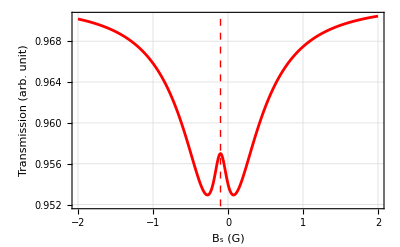

```mathematica
f[5,0.2,0]
```

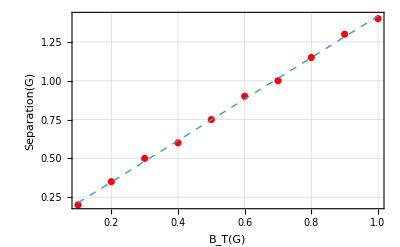

```mathematica
x={};
y={};
Do[
f[5,b,0];
t=Table[j,{j,-2,2,(2n+1)/200}];
tt1 = Table[{t[[i]],irho24[[i]]},{i,1, Length[table0]}];
posFilter= Select[tt1, 0<= #[[1]]<=2 &];
negFilter= Select[tt1, -2<= #[[1]]<=0 &];
diff = MinimalBy[posFilter, Last][[1,1]]-MinimalBy[negFilter, Last][[1,1]];
zeroFilter= Select[tt1, 0.0== #[[1]] &][[1,2]]-MinimalBy[posFilter, Last][[1,2]];
(*FWHM = Select[tt1, 0.0== #[[1]] &][[1,2]]-MinimalBy[posFilter, Last][[1,2]];*);
AppendTo[x,diff];
AppendTo[y,zeroFilter],
{b,Range[0.1, 1.0, 0.1]}

];
t1=Table[i,{i,0.1,1.0,0.1}];


t2=Table[{t1[[i]],x[[i]]},{i,1, Length[t1]}];
lm = LinearModelFit[t2,x1,x1];
paramText="Fit: y = "<>ToString[lm["BestFit"]];
p1=ListPlot[t2, PlotRange->All,Frame->True,PlotStyle->Red,FrameLabel->{"B_T(G)", "Separation(G)"},LabelStyle->Directive[Bold, Medium,Black],FrameTicks->{{True, None},{True,None}},GridLines->Automatic];
pp1 =Plot[lm[z],{z,0.1,1.0},PlotStyle->{Thin,Dashed}];
plt1 = Show[p1,pp1,PlotRange->All]
```

```mathematica
Export["/home/nayan/Desktop/diagrams/pdfs/sep_sngle.pdf",plt1,"PDF"]
```

/home/nayan/Desktop/diagrams/pdfs/sep_sngle.pdf

### Generating plots for Separation v/s B (TMF) and Relative Amplitude v/s B (TMF)

```mathematica
(* Generating plots for Separation and relative Amplitude v/s transverse B for the resonance at different power of Probe beam*)
ParallelDo[
Module[{plt1,,plt2,file1,file2},
x={};
y={};
Do[
f[a,b,0];
t=Table[j,{j,-2,2,(2n+1)/200}];
tt1 = Table[{t[[i]],irho24[[i]]},{i,1, Length[table0]}];
posFilter= Select[tt1, 0<= #[[1]]<=2 &];
negFilter= Select[tt1, -2<= #[[1]]<=0 &];
diff = MinimalBy[posFilter, Last][[1,1]]-MinimalBy[negFilter, Last][[1,1]];
zeroFilter= Select[tt1, 0.0== #[[1]] &][[1,2]]-MinimalBy[posFilter, Last][[1,2]];
(*FWHM = Select[tt1, 0.0== #[[1]] &][[1,2]]-MinimalBy[posFilter, Last][[1,2]];*);
AppendTo[x,diff];
AppendTo[y,zeroFilter],
{a,Range[1.0, 10.0, 0.5]}

];
t1=Table[i,{i,0.1,1.0,0.1}];


t2=Table[{t1[[i]],x[[i]]},{i,1, Length[t1]}];
lm = LinearModelFit[t2,x1,x1];
paramText="Fit: y = "<>ToString[lm["BestFit"]];
p1=ListPlot[t2, PlotRange->All,Frame->True,PlotStyle->Red,FrameLabel->{"B_T(G)", "Separation(G)"},LabelStyle->Directive[Bold, Medium,Black],FrameTicks->{{True, None},{True,None}},GridLines->Automatic];
pp1 =Plot[lm[z],{z,0.1,1.0},PlotStyle->{Thin,Dashed}];
plt1 = Show[p1,pp1,PlotRange->All];


t3=Table[{t1[[i]],y[[i]]},{i,1, Length[t1]}];
(*nlm = NonlinearModelFit[t3,α y1/(β +y1),{α,β},y1];
paramText1="Fit: y = "<>ToString[nlm["BestFit"]];
pp2 =Plot[nlm[z1],{z1,0.2,1.0},PlotStyle->{Thin,Dashed}];
plt2 = Show[p2,pp2,PlotRange->All];*);


plt2 = ListPlot[t3, PlotRange->All,Frame->True,PlotStyle->Red,FrameLabel->{"B_T(G)", "Relative Amp.(Arb. Unit)"},LabelStyle->Directive[Bold, Medium,Black],FrameTicks->{{True, None},{True,None}},GridLines->Automatic];




file1 =StringTemplate["/home/nayan/Desktop/theoretical/Hanlesystem/plots/onlyprobe/Seperation/plot_P_pr``.png"][b];
file2 =StringTemplate["/home/nayan/Desktop/theoretical/Hanlesystem/plots/onlyprobe/Amplitude/plot_P_pr``.png"][b];
Export[file1, plt1, ImageResolution->300];
Export[file2, plt2, ImageResolution->300]
],
{b, Range[0.1, 1.0, 0.1]}
]
```

### Generating plots for Population and transmission at various values of BTMF and probe power.

```mathematica
ParallelDo[
Module[{plt,filename},
plt = f[a,b,0];
filename =StringTemplate["/home/nayan/Desktop/theoretical/Hanlesystem/plots/onlyprobe/main/plot_P_pr``_B``.png"][a,b];
Export[filename, plt, ImageResolution->300]

],
{a,Range[1.0, 10.0, 0.5]},
{b, Range[0.1, 1.0, 0.1]}
]
```

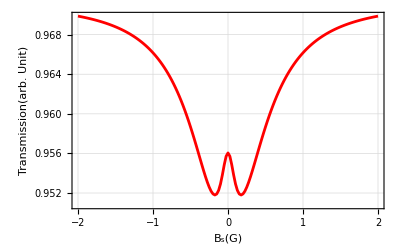

```mathematica
p=f[5,0.2,0]
```

```mathematica
Export["/home/nayan/Desktop/theoretical/Hanlesystem/plots/new/pic1.pdf",p, ImageResolution->300]
```

/home/nayan/Desktop/theoretical/Hanlesystem/plots/new/pic1.pdf